# Inlämningsuppgift 3: Matematisk modellering

IX1307 Problemlösning i Matematik, Inlämningsuppgift 3a, HT2017

Notebook mall av Göran Andersson

## 1. Inledning

Denna uppgift går ut på att lösa matematiska problem med hjälp av Mathematica och skriva en kort rapport direkt i en egen Notebook. Rapporten skall, för varje uppgift, beskriva: problemet, figur, ange namn på variabler, lösningen till problemet inklusive resonemang och sedan diskutera resultatet.

Plagiering är inte tillåten, och källor måste anges när ni referera till annat material. Lämna in både en pdf-fil och notebook-filen i Canvas. Pdf-filen behövs för plagiatkontroll, då *.nb inte är accepeterad i URKUND.

## 2. Nyttiga funktioner i Mathematica

#### Ekvationssystem

Solve kan användas för att lösa ekvationssystem genom att lägga in ekvationerna och variablerna i listor. Exempelvis kan ekvationssystemet:
2x-3y+4z=1
-x+2y-2z=2
3x+3y+4z=3
lösas med funktionen:

```mathematica
Solve[{2x-3y+4z==1, -x+2y-2z==2, 3x+3y+4z==3}, {x, y, z}]
```

{{x→-28,y→5,z→18}}

## 3. Problem

Lös nedanstående problem. Problemets lösning och resultat skall innehålla visualisering där det är relevant.
Tänk på följande:
1. Använd lämpliga stilar från meny Format->Style, i notebooken.
2. När ni skriver formler i text-celler, använd matematisk stil (se datorövning 1).
3. Glöm inte att ange namn och enhet för axlarna i grafer.

#### 1. Trafikflöde

Den här uppgiften går ut på och visa hur man kan använda linjära ekvationssystem för att studera trafikflödet genom ett trafiksystem. Trafiksystemet består av gator och korsningar där gatorna möts. Varje gata har ett visst flöde, som mäts i fordon per tidenhet. Vi skall beräkna trafikflödet för alla gatorna i trafiksystemet, givet flödet in till trafiksystemet.  Vi gör ett  viktigt antagande: Trafikflödet bevaras i varje korsning. Det betyder att ett fordon som når en korsning måste fortsätta genom trafiksystemet. Till exempel om flödet in till en fyrvägs korsning är x_1 fordon/tidsenhet respektive 30 fordon/tidsenhet och flödet ut från korsningen är x_2 fordon/tidsenhet respektive 50 fordon/tidsenhet, så gäller det att x_1+30=x_2+50 eller x_1-x_2=20. Varje korsning ger alltså en linjärekvation i okända flöden x_n. Om man löser ekvationssystemet så kan man bestämma flödet genom trafiksystemet.

a) Är vårt antagande om att flödet bevaras giltigt? När kan antagandet vara felaktigt?
Antagandet är felaktigt för x_1=0 och x_2=200 eftersom det till x_1 anslutna flödet ut (40) ej är anslutet till x_2.
b) Vilka andra förenklingar har vi antagit?

Studera motorvägssystemet i figur 1. Siffrorna anger trafikflödena i fordon per minut.
Enligt antagandet så måste x_1 leda ut i 3 olika flöden vilket endast kan förklaras med en 3 filig rondell där ingen motsatt trafik eller andra störningar äger rum. 
b) Ställ upp ekvationssystemet.

```mathematica
200==Subscript[x, 1]+Subscript[x, 2];
100==Subscript[x, 2]+Subscript[x, 3]-Subscript[x, 5];
60==Subscript[x, 5]+Subscript[x, 4];
40==Subscript[x, 1]-Subscript[x, 3]-Subscript[x, 4];
Piecewise[{{200==Subscript[x, 1]+Subscript[x, 2], □}, {100==Subscript[x, 2]+Subscript[x, 3]-Subscript[x, 5], □}, {60==Subscript[x, 5]+Subscript[x, 4], □}, {40==Subscript[x, 1]-Subscript[x, 3]-Subscript[x, 4], □}}]
```

c) Bestäm trafikflödet för vägsystemet.
Trafikflödet har flera heltalslösningar inom ett intervall för varje variabel.

```mathematica
NumberLinePlot[{Subscript[x, 1]-Subscript[x, 3]-Subscript[x, 4]==40,Subscript[x, 1]+Subscript[x, 2]==200,Subscript[x, 2]+Subscript[x, 3]-Subscript[x, 5]==100,Subscript[x, 4]+Subscript[x, 5]==60},{Subscript[x, 1],Subscript[x, 2],Subscript[x, 3],Subscript[x, 4],Subscript[x, 5]}]
```

-Graphics-

d) Hur ändras trafikflödet om  x_4 är noll ?
Om x_4=0 så måste x_5=60 för att flödet 60(ut) ska uppfyllas. Eftersom x_1 fortfarande kan tilldela x_5 så är detta den ända skillnaden. Tillåtna värden för x_1 är 40 ≤ x ≤ 200 och tillåtna värden på x_2 är 0 ≤ x_2 ≤ 160.
e) Antag att trafiken måste flyta i de riktningar som anges i figuren. Om x_4 är noll vad är då minsta värdet på x_1?
Om x_4=0 så måste x_1 ≥ 40 eftersom att flödet 40(ut) ändå måste uppfyllas.

figur 1. Trafikflöde i en motorvägskorsning

#### Kaniner

Leonardo av Pisa, även känd som Fibonacci (circa 1170-1250) skapade en av de äldsta matematiska modellerna av förökning. Han modellerade förökning av kaniner. Genom att modellera kaninpar kunde han undvika att ta hänsyn till individuella kaniner av olika kön. Modellen beskriver förökningen av kaniner från månad n=1 där p_n är antal kaniner vid månad n. När en kanin föds, så är den en unge under en månad och sedan förökar sig kaninparen varje månad. Antal kaniner kan då beskrivs av en differensekvation:

p_(n+2)=p_(n+1)+p_n

där vi antar att vi har bara ett kaninpar vid månad n=1, dvs intialvärdena är p_1=1 och p_2=1. Vilket betyder att p_3=2,  p_4=3 och p_5=5.

a) Beräkna talföljden och rita en graf över den.
Värdet av ett specifikt tal i talföljden är summan av de två föregående värdena i talföljden. Detta kan beskrivas med hjälp av rekursion:
p_n=p_(n-1)+p_(n-2) där n är det utvalda talet i talföljden.

```mathematica
l1=List[1,1,2,3,5,8,13,21,34,55,89,143,232,375,607,982];
```

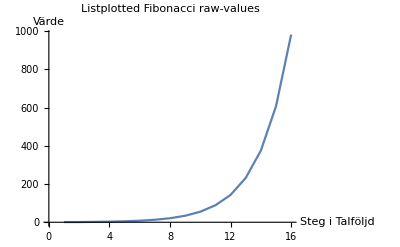

```mathematica
ListPlot[l1, Joined->True, AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel->"Listplotted Fibonacci raw-values"]
```

Ovan finns en lista med uträknade “råa” värden baserat på Fibonacci. Listan illustreras via funktionen “ListPlot” och för att länka samman punkterna so används argumentet “Joined”.

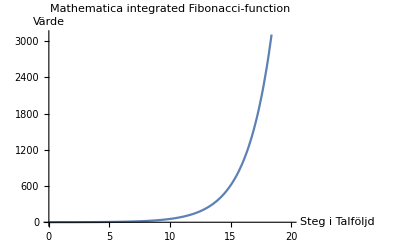

```mathematica
Plot[Fibonacci[n],{n,0,20},AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel ->"Mathematica integrated Fibonacci-function"]
```

Ovan illustreras Fibonaccis talföljd via Mathematicas inbyggda funktion “Fibonacci[ ]”.

```mathematica
f[x_]:=f[x]=f[x-1]+f[x-2];
f[0]=f[1]=1;
```

-Graphics-

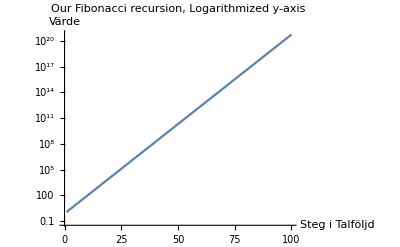

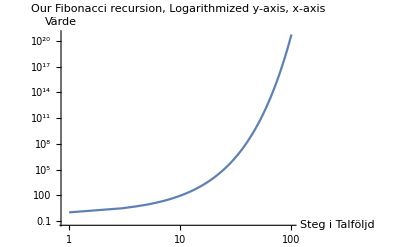

```mathematica
ListPlot[Array[f,100], Joined->True,AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel->"Our Fibonacci recursion"]
ListLogPlot[Array[f,100], Joined->True,AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel->"Our Fibonacci recursion, Logarithmized y-axis"]
ListLogLogPlot[Array[f,100], Joined->True,AxesLabel->{"Steg i Talföljd","Värde"},PlotLabel->"Our Fibonacci recursion, Logarithmized y-axis, x-axis"]
```

Ovan defineras först en rekursiv fuktion på Fibonaccis talföljd. Två startvärden tilldelas värdet 1. Genom funktionen “Array” skapas en lista baserat på den angivna funktionens värden som sedan illustreras genom “ListPlot”, “ListLogPlot”, “ListLogLogPlot”.

b) Undersök talföljden och diskutera tillväxtakten.
Tillväxten är exponentiell. Genom att betrakta talföjden så noteras en ökning för varje steg av summan av de två föregående värden i talföljden. För att talföljden ska vara giltig så initieras 1 som startvärde. Om det inte finns något värde innan 0 så kommer talföljden också få värdet 0 enligt dess definition(0+0=0...). Enligt antagandet så startar man med ett kaninpar som ej är könsmogna och därför återkommer värdet 1 i andra steget. Vid andra steget är kaninerna könsmogna och förökar sig därför till nästa steg 3(värde 2, ett könsmoget par och ett par ungar). I steg 4 så finns 2 könsmogna par men varav endast ett av paren har hunnit få ungar(värde 3, 2 par vuxna kaniner och 1 par ungar).  
c) Vilka begränsningar har modellen?
1. Kaniner får inte dö.
2. Det uppstår inga genetiska problem vid inavel.
3. Det föds varje månad en unge per könsmogen kanin.
4. Det finns endast ett kaninpar vid månad n = 1. 
d) Hur kan man förbättra modellen?